```mathematica
alpha:=Pi/6
alpha2:=Pi /2
th2:=Pi/6
M:=10^(-3)
m:=10^(-10)
m':=10^(-10)
omega:=2*Pi*10000
I1:=1
p:=1
mu0:=4*Pi*10^(-7)
A:=mu0*m*m'/(4*Pi)
g:=9.8
U[r_,th_]:=-A*(3*Sin[th]^2*Sin[th2]*Cos[alpha]*Sin[alpha-alpha2]+Sin[th2]*Sin[alpha2]+3*Sin[th]*Cos[th]*Cos[alpha]*Cos[th2])/r^3-r*Cos[th]*M*g+(I1/2)*(omega^2*Sin[th2]^2+p^2/I1^2)+M*r^2*Sin[th]^2*omega^2 /2
```

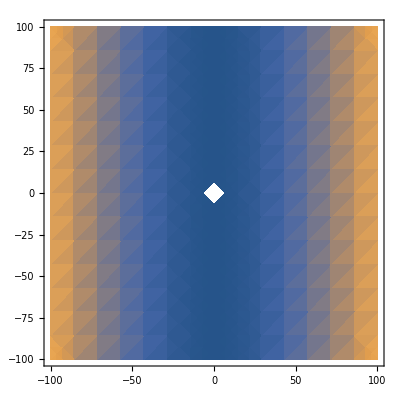

```mathematica
DensityPlot[U[Sqrt[x^2+y^2],ArcTan[x,y]-Pi/2],{x,-100,100},{y,-100,100}]
```